```mathematica
Clear[α,β,θ,ϵ,γ,μ,ω,η,ρ,ϕ,ζ,χ,ν,ψ,m,h,A,p]
```

```mathematica
(*Setting parameters*)
α=1;
β=0.00124;
θ=0.0000725;
μ=0.01;
λ=0.69219;
ρ=0.000023;
ζ=0.00000725;
ϕ=0.00125;
ψ=0.09;
γ=0.016;
ω=0.5;
η=0.025;
χ=0.1;
ν=0.1;
```

```mathematica
(*Calculation of equilibria for adaptive sex ratio*)
κ=γ*μ^2-η;
τ=(γ*(ρ-μ)*μ-η);
m=(α*ζ+θ*(ϕ+λ)-λ*ζ)/(β*ζ+(β*ζ*κ)/τ+θ*ψ*(1+κ/τ))
f=(κ*m)/τ
h=ν/χ-m/ω*κ
A=m/ω*κ
p=(ψ/β*(α-λ)-ϕ-λ)/(ζ+(ψ * θ)/β)
```

4.01794

4.01789

1.001

-0.00100448

4108.21

```mathematica
(*Calculation of eigenvalues of Jacobian for adaptive sex ratio*)
Eigenvalues[{{α-β*(m+f)-θ*p-λ,-β*h,-β*h,0,-θ*h},{0,γ*m*μ^2-ω*A-η*m,γ*f*μ^2-η*f,-ω*f,0},{0,γ*m*μ*(ρ-μ)-η*m,γ*f*μ*(ρ-μ)-ω*A-η*f,-ω*m,0},{0,ψ*A,ψ*A,ψ*(m+f)-ϕ-λ-ζ*p,-ζ*A},{χ*p,0,0,χ*p,χ*(h+A)-ν}}]
```

{-4.60569+0. ⅈ,3.97773+0. ⅈ,-0.0170974+1.17135 ⅈ,-0.0170974-1.17135 ⅈ,0.66215+0. ⅈ}

```mathematica
{-0.009049216386680325+6.963095092485391 ⅈ,-0.009049216386680325-6.963095092485391 ⅈ,-4.644941336593321+0. ⅈ,3.9776701130922922+0. ⅈ,0.6853696562743916+0. ⅈ}
```

{-0.00904922+6.9631 ⅈ,-0.00904922-6.9631 ⅈ,-4.64494+0. ⅈ,3.97767+0. ⅈ,0.68537+0. ⅈ}

```mathematica
{-0.002025406927785577+0.23535983617021258ⅈ,-0.002025406927785577-0.23535983617021258ⅈ,0.021021173056817846+0.18200132227873367 ⅈ,0.021021173056817846-0.18200132227873367 ⅈ,-0.037991532258064516+0. ⅈ}
```

{-0.00202541+0.23536 ⅈ,-0.00202541-0.23536 ⅈ,0.0210212+0.182001 ⅈ,0.0210212-0.182001 ⅈ,-0.0379915+0. ⅈ}

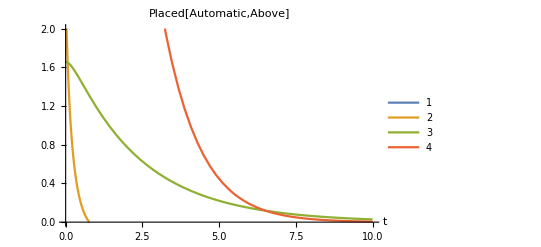

```mathematica
(*Long-term equilibria for adaptive sex ratio*)
Clear[m,f,h,A,p,t]
tf=10;
q=NDSolve[{h'[t]==α*h[t]*-β*h[t]*(m[t]+f[t])-θ*p[t]*h[t]-λ*h[t],f'[t]==γ*m[t]*f[t]*μ^2-ω*m[t]*A[t]-η*m[t]*f[t],m'[t]==γ*m[t]*f[t]*μ*(ρ-μ)-ω*m[t]*A[t]-η*m[t]*f[t],A'[t]==ψ*A[t]*(m[t]+f[t])-ϕ*A[t]-λ*A[t]-ζ*p[t]*A[t],p'[t]==χ*p[t]*(h[t]+A[t])-ν*p[t],h[0]==3.457031250000002,m[0]==5.514322916666665,f[0]==2.3632812499999996,A[0]==1.6542968749999998,p[0]==17.194010416666664},{m,f,A,p},{t,tf}];
Plot[Evaluate[{m[t],f[t],A[t],p[t]}/.q],{t,0,tf},PlotStyle->Automatic,PlotRange->{0,2},AxesLabel->{"t",""},PlotLabel->Placed[Automatic, Above],PlotLegends->Automatic]
Evaluate[{h[tf],m[tf],f[tf],A[tf],p[tf]}/.q];
```

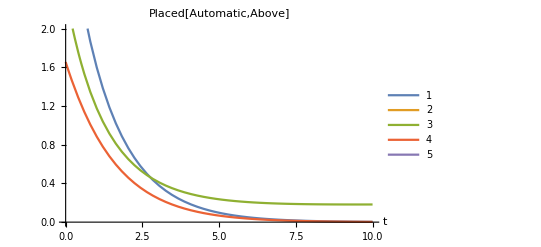

-Graphics-

```mathematica
(*Calculation of equilibria for 50:50 sex ratio*)
κ=γ*μ^2-η;
m=((ϕ*θ)/ζ+α*(1-ν/(χ*σ)))/(β+ϵ+(2*θ*ψ)/ζ-(α*κ)/(ω*σ))
f=m
h=ν/χ-(m*κ)/ω
A=(m*κ)/ω
p=(2*ψ*m-ϕ)/ζ
```

(1.0125-9./σ)/(1.80124+ϵ+9.9/σ)

(1.0125-9./σ)/(1.80124+ϵ+9.9/σ)

9.+(9.9 (1.0125-9./σ))/(1.80124+ϵ+9.9/σ)

-(9.9 (1.0125-9./σ))/(1.80124+ϵ+9.9/σ)

137931. (-0.00125+(0.18 (1.0125-9./σ))/(1.80124+ϵ+9.9/σ))

```mathematica
(*Calculation of eigenvalues of Jacobian for 50/50 sex ratio*)
Eigenvalues[{{α-2*α*h/σ-β*m-ϵ*f-θ*p,-ϵ*h,-β*h,0,-θ*h},{0,γ*m*μ^2-ω*A-η*m,γ*f*μ^2-η*f,-ω*f,0},{0,γ*m*μ^2-η*m,γ*f*μ^2-ω*A-η*f,-ω*m,0},{0,ψ*A,ψ*A,ψ*(m+f)-ϕ-ζ*p,-ζ*A},{χ*p,0,0,χ*p,χ*(h+A)-ν}}]
```

{1/σ 1. Root[6.04329×10^-14 σ^4+4.25913×10^-10 σ^5+1.20989×10^-10 ϵ σ^5+(2.85909×10^-8 σ^3-2.17764×10^-6 σ^4-1.1459×10^-6 ϵ σ^4) #1+(-0.000151447 σ^2-0.0205845 σ^3-0.000303943 ϵ σ^3) #1^2+(-1.38577 σ+0.512314 σ^2-2.78114 ϵ σ^2) #1^3+(2.00201-1.38936 σ+4.01789 ϵ σ) #1^4+1. #1^5&,1],1/σ 1. Root[6.04329×10^-14 σ^4+4.25913×10^-10 σ^5+1.20989×10^-10 ϵ σ^5+(2.85909×10^-8 σ^3-2.17764×10^-6 σ^4-1.1459×10^-6 ϵ σ^4) #1+(-0.000151447 σ^2-0.0205845 σ^3-0.000303943 ϵ σ^3) #1^2+(-1.38577 σ+0.512314 σ^2-2.78114 ϵ σ^2) #1^3+(2.00201-1.38936 σ+4.01789 ϵ σ) #1^4+1. #1^5&,2],1/σ 1. Root[6.04329×10^-14 σ^4+4.25913×10^-10 σ^5+1.20989×10^-10 ϵ σ^5+(2.85909×10^-8 σ^3-2.17764×10^-6 σ^4-1.1459×10^-6 ϵ σ^4) #1+(-0.000151447 σ^2-0.0205845 σ^3-0.000303943 ϵ σ^3) #1^2+(-1.38577 σ+0.512314 σ^2-2.78114 ϵ σ^2) #1^3+(2.00201-1.38936 σ+4.01789 ϵ σ) #1^4+1. #1^5&,3],1/σ 1. Root[6.04329×10^-14 σ^4+4.25913×10^-10 σ^5+1.20989×10^-10 ϵ σ^5+(2.85909×10^-8 σ^3-2.17764×10^-6 σ^4-1.1459×10^-6 ϵ σ^4) #1+(-0.000151447 σ^2-0.0205845 σ^3-0.000303943 ϵ σ^3) #1^2+(-1.38577 σ+0.512314 σ^2-2.78114 ϵ σ^2) #1^3+(2.00201-1.38936 σ+4.01789 ϵ σ) #1^4+1. #1^5&,4],1/σ 1. Root[6.04329×10^-14 σ^4+4.25913×10^-10 σ^5+1.20989×10^-10 ϵ σ^5+(2.85909×10^-8 σ^3-2.17764×10^-6 σ^4-1.1459×10^-6 ϵ σ^4) #1+(-0.000151447 σ^2-0.0205845 σ^3-0.000303943 ϵ σ^3) #1^2+(-1.38577 σ+0.512314 σ^2-2.78114 ϵ σ^2) #1^3+(2.00201-1.38936 σ+4.01789 ϵ σ) #1^4+1. #1^5&,5]}

```mathematica
Clear[m,f,h,A,p,t]
```

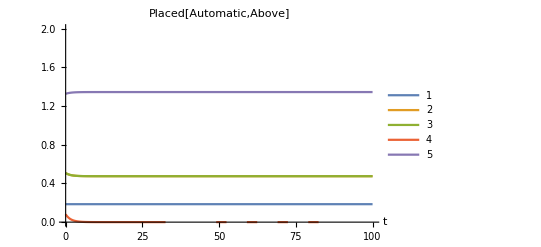

```mathematica
(*Long-term equilibria for 50:50 sex ratio*)
tf=100;
q=NDSolve[{f'[t]==γ*m[t]*f[t]*μ^2-ω*m[t]*A[t],m'[t]==γ*m[t]*f[t]*μ^2-ω*m[t]*A[t],A'[t]==ψ*A[t]*(m[t]+f[t])-λ*A[t]-ζ*p[t]*A[t],p'[t]==χ*p[t]*(α+A[t])-ν*p[t],h[0]==0.185451,m[0]==0.5076,f[0]==0.5076,A[0]==0.0812161,p[0]==1.326},{h,m,f,A,p},{t,tf}];
Plot[Evaluate[{h[t],m[t],f[t],A[t],p[t]}/.q],{t,0,tf},PlotStyle->Automatic,PlotRange->{0,2},AxesLabel->{"t",""},PlotLabel->Placed[Automatic, Above],PlotLegends->Automatic]
Evaluate[{h[tf],m[tf],f[tf],A[tf],p[tf]}/.q];
```